#### BDM

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Hector\Desktop\MacDesktop\BDM\Mathematica

```mathematica
(*Import["D5.m"]

reducedD2=<<"reducedD2.m"; Use this reduced below, not D5!*)
```

```mathematica
reducedD2=<<"squares2Dsize1to4.m";
```

```mathematica
Length[reducedD2]
```

66066

```mathematica
Table[With[{sq=reducedD2[[nS]]},HashSquares[sq[[1]]]=sq[[2]]],{nS,Length@reducedD2}];
```

```mathematica
(*D5=Select[{ToExpression/@StringSplit[#⟦1⟧,""],-Log[2,#⟦2⟧]}&/@<<"D5.m",Length[#⟦1⟧]≤12&];

completedD5=Join[D5,Flatten[#,1]&/@Thread[{List/@Complement[Tuples[{0,1},12],First/@D5],Max[(Last/@D5)]+1}]];

Table[With[{sq=completedD5[[nS]]},HashStrings[sq[[1]]]=sq[[2]]],{nS,Length@completedD5}];

BDM[array_,dim_]:=First[Module[{part=Partition[array,{dim,dim}]},Total[{Log[2,#[[2]]]+#[[1]]}&/@({HashSquares[#[[1]]],#[[2]]}&/@Tally[Flatten[part,1]])]]]*)
```

```mathematica
(*BDM[array_,dim_]:=If[TrueQ[Min[Dimensions[array]]<dim],Log[2,Times@@Dimensions[array]],First[Module[{part=Partition[array,{dim,dim}]},Total[{Log[2,#[[2]]]+#[[1]]}&/@({HashSquares[#[[1]]],#[[2]]}&/@Tally[Flatten[part,1]])]]]]*)
```

```mathematica
Clear[reducedD2]
```

```mathematica
BDM[array_,dim_Integer]:=If[TrueQ[Min[Dimensions[array]]<dim],BDM[array,Min[Dimensions[array]]],First[Block[{part=Partition[array,{dim,dim}]},Total[{Log[2,#[[2]]]+#[[1]]}&/@({HashSquares[#[[1]]],#[[2]]}&/@Tally[Flatten[part,1]])]]]]
```

#### Normalized BDM

Gives the maximum product of k natural numbers which sum n.

```mathematica
MaxProduct[n_,k_]:=With[{f = Floor[n/k]},(f^(k-n+(f k)))((f+1)^(n-(f k)))]
```

```mathematica
decreasingComplex = Reverse@Sort[Last/@ reducedD2];
```

Sum of the n more complex squares:

```mathematica
sumComplexUpTo= FoldList[N@(#1+#2) &,decreasingComplex[[1]], Rest@decreasingComplex];
```

Given the size (edge) of a square array, calculate the maximum BDM value:
Only for size 4

```mathematica
MaxBDMold[n_]:= 
Plus@@decreasingComplex[[1;;Min[Floor[n/4]^2,2^16]]]+Log[2,MaxProduct[Floor[n/4]^2, Min[Floor[n/4]^2,2^16] ]];
```

```mathematica
MaxBDM[n_]:=
sumComplexUpTo[[Min[Floor[n/4]^2,2^16]]]+Log[2,MaxProduct[Floor[n/4]^2, Min[Floor[n/4]^2,2^16] ]];
```

#### Minimum value for BDM

```mathematica
MinBDM[n_]:= 
Last@decreasingComplex+ Log[2,Floor[n/4]^2]
```

#### Normalization

A variant of the NBDM that considers minimum and maximum

```mathematica
NBDM[array_]:=
N@Rescale[BDM[array,4],{MinBDM[Length@array],MaxBDM[Length@array]}]
```

#### Example

These are the 4 most complex square arrays in 4x4:

```mathematica
s4q = First/@Reverse[SortBy[reducedD2,Last]][[1;;4]]
```

{{{1,1,1,0},{0,0,1,0},{0,1,1,1},{1,0,0,0}},{{1,1,1,0},{0,0,0,1},{1,0,1,1},{1,0,0,0}},{{1,1,0,1},{0,0,0,1},{0,1,0,1},{0,1,1,0}},{{1,0,1,1},{1,0,0,0},{1,0,1,0},{0,1,1,0}}}

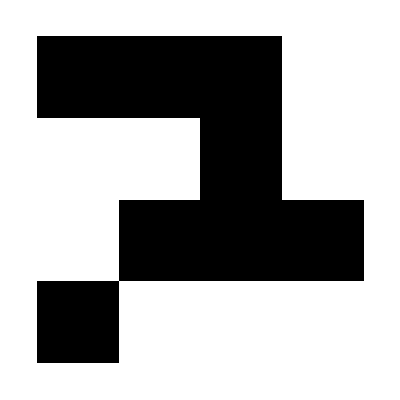
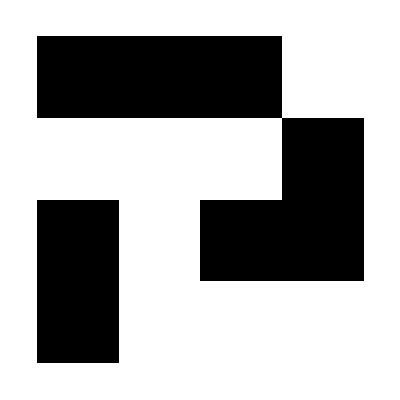
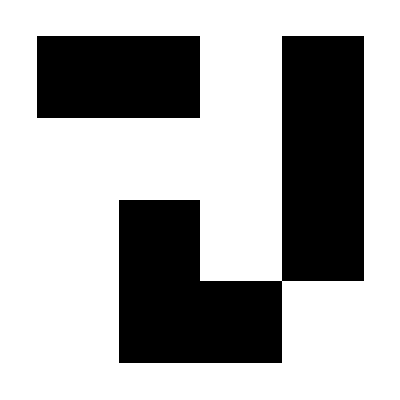
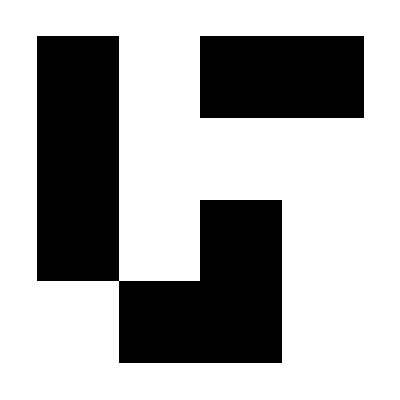

```mathematica
ArrayPlot/@ s4q
```

Now we combine them in just one array:

```mathematica
a12 ={{1,1,1,0,1,1,1,0},{0,0,1,0,0,0,0,1},{0,1,1,1,1,0,1,1},{1,0,0,0,1,0,0,0},{1,1,0,1,1,0,1,1},{0,0,0,1,1,0,0,0},{0,1,0,1,1,0,1,0},{0,1,1,0,0,1,1,0}};
```

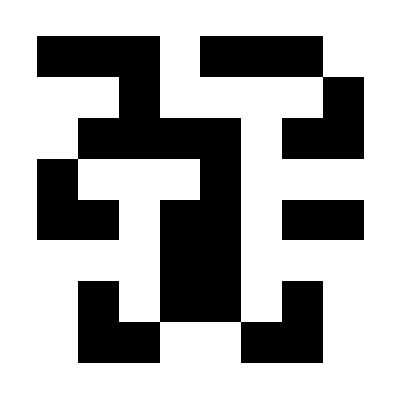

```mathematica
ArrayPlot@a12
```

Now we can produce values from 0 to 1.

```mathematica
BDM[a12,4] //N
```

144.091

```mathematica
NBDM[a12]
```

1.

```mathematica
NBDM[Table[0,{12},{12}]]
```

0.0614302

```mathematica
makeString[array_]:=StringDrop[StringJoin[StringJoin/@((Function[u,(ToString /@ u)<>"-"])/@ array)],-1]
```